```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}],{{1,m},{m,1}}]->t]
```

```mathematica
β[ω,δ,t,ϵ,10]//MatrixForm
```

(ⅈ δ-ϵ+ω | -t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -t
-t | ⅈ δ-ϵ+ω | -t | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -t | ⅈ δ-ϵ+ω | -t | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -t | ⅈ δ-ϵ+ω | -t | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -t | ⅈ δ-ϵ+ω | -t | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ+ω | -t | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ+ω | -t | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ+ω | -t | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ+ω | -t
-t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ+ω)

```mathematica
Clear[β]
```

```mathematica
T[t_,m_]:=T[t,m]=ReplacePart[0*IdentityMatrix[m],Join[Table[{x,x+1},{x,Range[1,m,4]}],Table[{x,x-1},{x,Range[4,m,4]}]]->t]
```

```mathematica
T[t,10]//MatrixForm
```

(0 | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | t | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | t | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | t | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Clear[leadgenerateleft]
```

```mathematica
leadgenerateleft[ω_,δ_,t_,ϵ_,m_]:= leadgenerateleft[ω,δ,t,ϵ,m]= Module[{unit=Inverse[β[ω,δ,t,ϵ,m]],J=Inverse[β[ω,δ,t,ϵ,m]]},Do[J= Inverse[IdentityMatrix[m]-unit.T[t,m].J.ConjugateTranspose[T[t,m]]].unit,3000];J=J]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-Inverse[β[ω,δ,t,ϵ,m]].T[t,m].leadgenerateleft[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-Inverse[β[ω,δ,t,ϵ,m]].T[t,m].leadgenerateleft[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].SR[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].SL[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,m_]:= If[Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]-T[t,m].GNON[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].GNON[ω,δ,t,ϵ,m]]]>60,60,Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]-T[t,m].GNON[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].GNON[ω,δ,t,ϵ,m]]]]
```

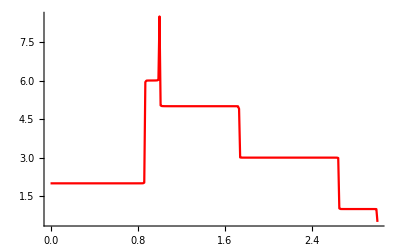

```mathematica
Monitor[Show[ListLinePlot[Table[{ω,(*Print["working on "<>ToString[ω]<>"..."];*)tr1[ω,0.001,1,0,12]},{ω,Range[0,3,0.01]}],PlotStyle->Red],PlotRange->All],ω]
```

```mathematica
Clear[dist]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,12]],total(*concentration*)],RandomSample[Join[s[1,100,7,12]],0*(total-concentration)]],First],1000]
```

```mathematica
dist[30,15][[1]]
```

{{2,10},{4,3},{8,5},{14,9},{15,12},{17,2},{41,4},{41,6},{44,6},{47,11},{48,9},{50,9},{50,10},{53,5},{58,9},{59,11},{60,6},{63,5},{73,7},{76,6},{76,11},{77,4},{77,8},{79,7},{86,8},{87,2},{87,11},{88,9},{90,1},{94,8}}

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,unitcell_,total_,concentration_,number_]:=Inverse[Module[{J=β[ω,δ,t,ϵ,12]},Do[J=Module[{m=unitcell,abc=dist[total,concentration][[number]]},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]]
```

```mathematica
device[ω_,δ_,t_,ϵ_,ϵ1_,m_,total_,concentration_,number_]:=Module[{list,b2},
sl1= Module[{J=SL[ω,0.001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number].T[t,m].J.ConjugateTranspose[T[t,m]]].f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number],{unitcell,1,100}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.ConjugateTranspose[T[t,m]].leadgenerateleft[ω,0.001,1,0,m].ConjugateTranspose[T[t,m]]].sl1;
Ir1:=Inverse[IdentityMatrix[m]-leadgenerateleft[ω,0.001,1,0,m].ConjugateTranspose[T[t,m]].sl1.ConjugateTranspose[T[t,m]]].leadgenerateleft[ω,0.001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.001,1,0,m].ConjugateTranspose[T[t,m]].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];tra=Abs[Tr[gdd1.T[t,m].grr1.ConjugateTranspose[T[t,m]]-T[t,m].GNON1.ConjugateTranspose[T[t,m]].GNON1]];If[tra>6,6,tra]]
```

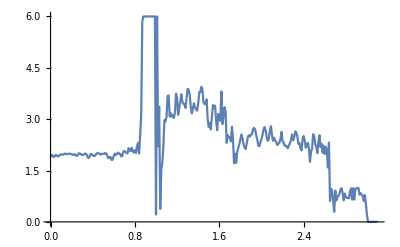

```mathematica
Table[{ω,device[ω,0.001,1,0,0.5,12,20,25,11]},{ω,Range[0,3.1,0.01]}]//ListLinePlot
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/12ZGribbon.dat",Table[{ω,device[ω,0.001,1,0,0.5,12,20,25,11]},{ω,Range[0,3,0.01]}]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/12ZGribbon.dat

```mathematica
ListLinePlot[Table[{ω,device[ω,0.001,1,0,0.5,16,40,25,11]},{ω,Range[0,3,0.01]}],PlotRange->All,PlotStyle->Red]
```

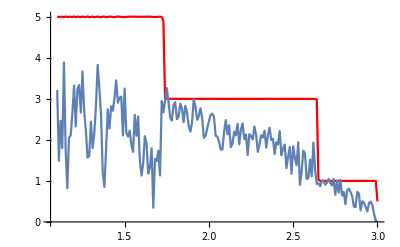

```mathematica
Show[%39,%35]
```

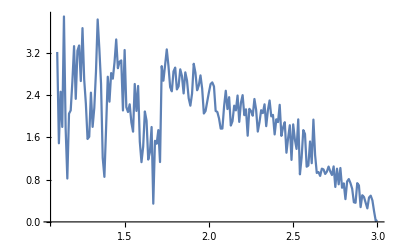

```mathematica
%35
```

```mathematica
Export["/home/shardulmukim/PhD/invited/CNT/pris_12_.dat",Table[{ω,device[-ω,0.001,1,0,0,12,25,25,11]},{ω,Range[1.1,3,0.01]}]]
```

/home/shardulmukim/PhD/invited/CNT/pris_12_.dat

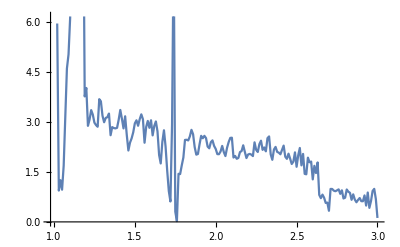

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/invited/CNT/input_N25.dat"]]
```

```mathematica
LaunchKernels[4]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
Table[Export["/home/shardulmukim/PhD/fwi/CNT/CA_CONC_"<>ToString[x]<>"_.dat",Print[x];Table[{ω,Mean[ParallelTable[device[ω,0.001,1,0,1,12,x,0,n],{n,700}]]},{ω,Range[-3,3,0.01]}]],{x,Range[10,100,10]}]
```

10

20

30

40

50

60

70

80

$Aborted

```mathematica
Range[5,50,5]
```

{5,10,15,20,25,30,35,40,45,50}

```mathematica
transmission=Table[{num,Import["/home/shardulmukim/PhD/fwi/CNT/CA_CONC_"<>ToString[num]<>"_.dat"]},{num,Range[10,70,10]}]
```

{{10,{{-3.,0.154077},{-2.99,0.633369},{-2.98,0.699945},{-2.97,0.736062},{-2.96,0.767023},{-2.95,0.778571},{-2.94,0.808479},{-2.93,0.817817},{-2.92,0.827439},{-2.91,0.842372},{-2.9,0.852227},{-2.89,0.868353},{-2.88,0.873197},576,{2.89,0.460277},{2.9,0.465532},{2.91,0.451676},{2.92,0.452502},{2.93,0.43665},{2.94,0.439046},{2.95,0.431902},{2.96,0.428119},{2.97,0.400299},{2.98,0.380355},{2.99,0.367718},{3.,0.238241}}},5,{70,{1}}}
 |  |  |  |

```mathematica
input = Table[ParallelTable[{ω,device[ω,0.001,1,0,1,12,30,0,num]},{ω,Range[-3,3,0.01]}],{num,100}]
```

{{{-3.,0.0222475},{-2.99,0.0194911},{-2.98,0.0340749},{-2.97,0.0244364},{-2.96,0.714698},{-2.95,0.613504},{-2.94,0.296943},{-2.93,0.987237},{-2.92,0.657479},{-2.91,0.763617},{-2.9,0.911681},{-2.89,0.313399},{-2.88,1.04565},576,{2.89,0.151601},{2.9,0.199715},{2.91,0.219788},{2.92,0.294049},{2.93,0.484875},{2.94,0.781541},{2.95,0.213808},{2.96,0.164769},{2.97,0.166942},{2.98,0.124263},{2.99,0.0884327},{3.,0.0142975}},98,{1}}
 |  |  |  |

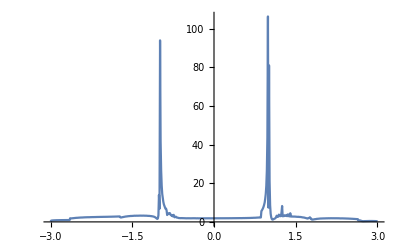

```mathematica
ListLinePlot[transmission[[1,2]],PlotRange->All]
```

```mathematica
Dimensions[transmission]
```

{10,2}

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],Module[{B1=Transpose[{m5[[1;;601]][[;;,1]],(m5[[1;;601,2]]-transmission[[con,2]][[1;;601,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{con,7}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
misfit[3,-3,1]
```

{{{10,2.06537},{20,2.40433},{30,1.72766},{40,1.73098},{50,1.6532},{60,3.24167},{70,2.13693}},{50,1.6532}}

```mathematica
Table[misfit[-1.2,-3,n][[2]][[1]],{n,100}]
```

{50,50,10,10,10,40,10,10,30,10,50,10,40,10,50,10,10,10,30,10,40,10,10,40,30,50,10,10,50,10,30,30,10,10,70,30,40,10,10,50,40,10,10,30,10,50,30,50,50,50,70,50,10,30,50,10,30,10,40,30,10,30,10,40,50,40,50,10,30,10,30,10,30,40,10,10,10,10,50,10,10,30,30,50,30,10,10,30,10,50,30,30,50,10,50,50,10,50,50,50}

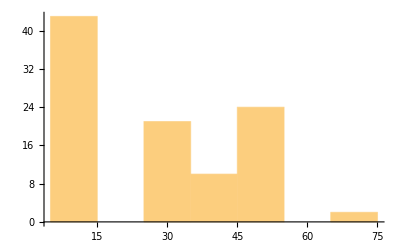

```mathematica
Histogram[%130]
```

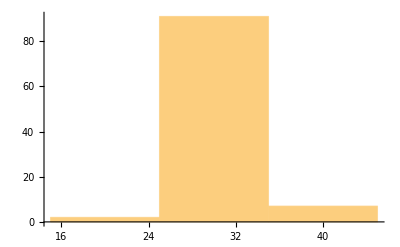

```mathematica
Histogram[%128]
```

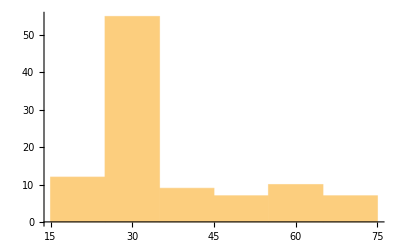

```mathematica
Histogram[%124]
```

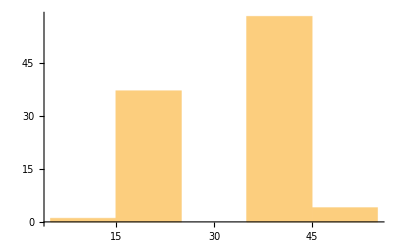

```mathematica
Histogram[%120]
```

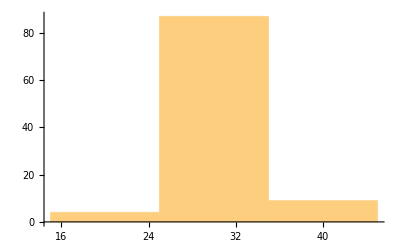

```mathematica
Histogram[%118]
```

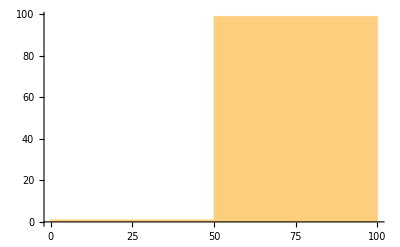

```mathematica
Histogram[%112]
```

```mathematica
Histogram[%110]
```

-Graphics-

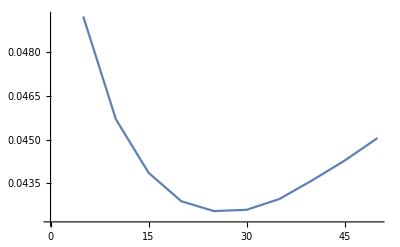

```mathematica
ListLinePlot[misfit[2.99,1.4,1][[1]]]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/CNT/misfit_N25.dat",misfit[2.99,1.4,1][[1]]]
```

/home/shardulmukim/PhD/fwi/CNT/misfit_N25.dat

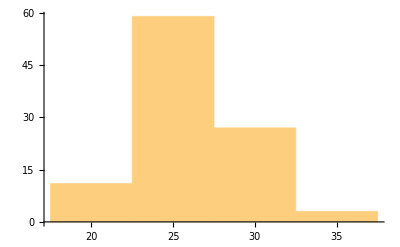

```mathematica
Histogram[%47]
```

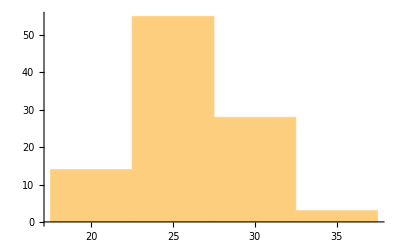

```mathematica
Histogram[%43]
```

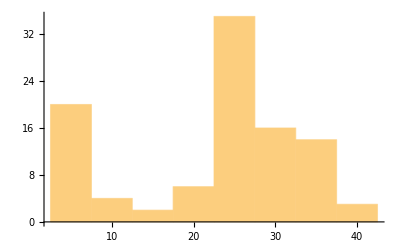

```mathematica
Histogram[%40]
```

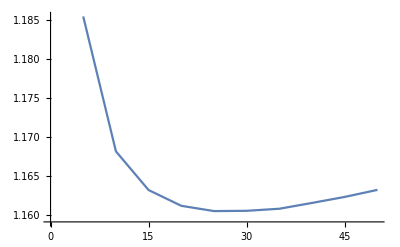

```mathematica
ListPlot[%33,Joined->True]
```

```mathematica
Range[1,10,3]
```

{1,4,7,10}

```mathematica
trainingset[ω_]:=Table[5+10*(n-1)->transmission[[n]][[ω*100+1,2]],{n,Range[1,10,1]}]
```

```mathematica
data[num_,ω_]:=Module[{P},P=Predict[trainingset[ω],Method->"NeuralNetwork"]; P[num]]
```

```mathematica
(*This allows us to generate average specta for continuous number of impurities *)
```

```mathematica
data[50,3]//AbsoluteTiming
```

{4.53691,0.239441}

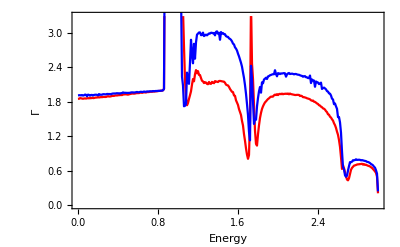

```mathematica
Show[ListLinePlot[transmission[[10]],PlotStyle->Red,Frame->True,PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]],FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]}],ListLinePlot[Table[{ω,data[50,ω]},{ω,Range[0,3,0.01]}],PlotStyle->Blue]]
```

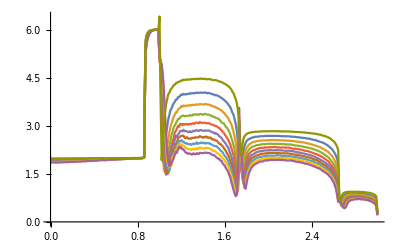

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/fwi/CNT/*.dat"],PlotRange->All]
```

```mathematica
Table[{ω,tr1[ω,0.001,1,0,12]},{ω,Range[1.02,3,0.01]}]
```

{{1.02,5.00804},{1.03,5.00355},{1.04,5.00198},{1.05,5.00125},{1.06,5.00086},{1.07,5.00063},{1.08,5.00049},{1.09,5.00038},{1.1,5.0003},{1.11,5.00024},{1.12,5.00019},{1.13,5.00016},{1.14,5.00014},{1.15,5.00013},{1.16,5.00011},{1.17,5.00009},{1.18,5.00007},{1.19,5.00006},{1.2,5.00007},{1.21,5.00006},{1.22,5.00004},{1.23,5.00003},{1.24,5.00004},{1.25,5.00005},{1.26,5.00003},{1.27,5.00002},{1.28,5.00003},{1.29,5.00003},{1.3,5.00001},{1.31,5.00002},{1.32,5.00002},{1.33,5.},{1.34,5.00002},{1.35,5.00001},{1.36,5.00001},{1.37,5.00001},{1.38,5.},{1.39,5.00001},{1.4,5.},{1.41,5.00001},{1.42,5.},{1.43,5.},{1.44,5.},{1.45,4.99999},{1.46,5.00001},{1.47,5.},{1.48,4.99999},{1.49,5.},{1.5,5.},{1.51,4.99998},{1.52,4.99999},{1.53,5.},{1.54,5.},{1.55,4.99999},{1.56,4.99999},{1.57,4.99998},{1.58,4.99998},{1.59,4.99997},{1.6,4.99997},{1.61,4.99997},{1.62,4.99996},{1.63,4.99996},{1.64,4.99995},{1.65,4.99993},{1.66,4.9999},{1.67,4.99987},{1.68,4.99982},{1.69,4.99972},{1.7,4.99952},{1.71,4.99898},{1.72,4.99658},{1.73,4.89891},{1.74,3.00782},{1.75,3.00154},{1.76,3.00064},{1.77,3.00034},{1.78,3.00021},{1.79,3.00015},{1.8,3.00011},{1.81,3.00008},{1.82,3.00006},{1.83,3.00005},{1.84,3.00004},{1.85,3.00003},{1.86,3.00003},{1.87,3.00003},{1.88,3.00002},{1.89,3.00002},{1.9,3.00002},{1.91,3.00001},{1.92,3.00002},{1.93,3.00001},{1.94,3.00001},{1.95,3.00001},{1.96,3.00001},{1.97,3.},{1.98,3.},{1.99,3.},{2.,3.},{2.01,3.},{2.02,3.},{2.03,3.00001},{2.04,3.00001},{2.05,3.},{2.06,3.},{2.07,3.},{2.08,3.},{2.09,3.},{2.1,3.},{2.11,3.},{2.12,3.},{2.13,3.},{2.14,3.},{2.15,3.},{2.16,3.},{2.17,3.},{2.18,3.},{2.19,3.},{2.2,3.},{2.21,3.},{2.22,3.},{2.23,3.},{2.24,3.},{2.25,3.},{2.26,3.},{2.27,3.},{2.28,3.},{2.29,3.},{2.3,3.},{2.31,3.},{2.32,3.},{2.33,3.},{2.34,3.},{2.35,3.},{2.36,3.},{2.37,3.},{2.38,3.},{2.39,2.99999},{2.4,2.99999},{2.41,2.99999},{2.42,2.99999},{2.43,2.99999},{2.44,2.99999},{2.45,2.99999},{2.46,2.99999},{2.47,2.99999},{2.48,2.99998},{2.49,2.99998},{2.5,2.99998},{2.51,2.99998},{2.52,2.99997},{2.53,2.99997},{2.54,2.99996},{2.55,2.99995},{2.56,2.99994},{2.57,2.99992},{2.58,2.99989},{2.59,2.99984},{2.6,2.99977},{2.61,2.99962},{2.62,2.99926},{2.63,2.99801},{2.64,2.98526},{2.65,1.02664},{2.66,1.00246},{2.67,1.00085},{2.68,1.00043},{2.69,1.00025},{2.7,1.00017},{2.71,1.00012},{2.72,1.00009},{2.73,1.00007},{2.74,1.00005},{2.75,1.00004},{2.76,1.00003},{2.77,1.00003},{2.78,1.00002},{2.79,1.00002},{2.8,1.00002},{2.81,1.00001},{2.82,1.00001},{2.83,1.00001},{2.84,1.},{2.85,1.},{2.86,0.999999},{2.87,0.999996},{2.88,0.999993},{2.89,0.999989},{2.9,0.999984},{2.91,0.999978},{2.92,0.999969},{2.93,0.999957},{2.94,0.999938},{2.95,0.999908},{2.96,0.999852},{2.97,0.999731},{2.98,0.999387},{2.99,0.997535},{3.,0.500118}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/CNT/pris_12_.dat",%61]
```

/home/shardulmukim/PhD/fwi/CNT/pris_12_.dat

```mathematica
Table[input[[2]][[x]],{x,103,301}]
```

{{1.02,5.94423},{1.03,0.939051},{1.04,1.25003},{1.05,0.96474},{1.06,1.68482},{1.07,3.15377},{1.08,4.59579},{1.09,5.01971},{1.1,6.11525},{1.11,10.5244},{1.12,48.0531},{1.13,42.3646},{1.14,22.1694},{1.15,12.2637},{1.16,28.8765},{1.17,1205.03},{1.18,10.6517},{1.19,3.76008},{1.2,4.01249},{1.21,2.87853},{1.22,3.06634},{1.23,3.34962},{1.24,3.21623},{1.25,2.9746},{1.26,2.90079},{1.27,2.85086},{1.28,3.67781},{1.29,3.61325},{1.3,3.18184},{1.31,2.98576},{1.32,3.11618},{1.33,3.13679},{1.34,3.24629},{1.35,2.59725},{1.36,2.84016},{1.37,2.81143},{1.38,2.80181},{1.39,2.8192},{1.4,3.05946},{1.41,3.35378},{1.42,3.09181},{1.43,2.80097},{1.44,3.16452},{1.45,2.60918},{1.46,2.13922},{1.47,2.37396},{1.48,2.50217},{1.49,2.68362},{1.5,2.95277},{1.51,3.04386},{1.52,2.87983},{1.53,3.07647},{1.54,3.22282},{1.55,3.07564},{1.56,2.37167},{1.57,2.84321},{1.58,3.02568},{1.59,2.81804},{1.6,3.04517},{1.61,2.5923},{1.62,2.87335},{1.63,3.01011},{1.64,2.71273},{1.65,2.0058},{1.66,1.75129},{1.67,2.39643},{1.68,2.74568},{1.69,2.25669},{1.7,1.53716},{1.71,0.923297},{1.72,0.612009},{1.73,2.91552},{1.74,8.24993},{1.75,0.307801},{1.76,0.0222811},{1.77,1.4418},{1.78,1.43264},{1.79,1.69262},{1.8,1.92886},{1.81,2.45646},{1.82,2.46051},{1.83,2.44081},{1.84,2.5605},{1.85,2.75846},{1.86,2.62739},{1.87,2.23901},{1.88,2.01398},{1.89,2.03553},{1.9,2.32467},{1.91,2.57889},{1.92,2.50685},{1.93,2.57868},{1.94,2.51132},{1.95,2.25675},{1.96,2.20541},{1.97,2.38816},{1.98,2.4427},{1.99,2.27771},{2.,2.18598},{2.01,2.03092},{2.02,2.02828},{2.03,2.11011},{2.04,2.27658},{2.05,2.09252},{2.06,1.97231},{2.07,2.2206},{2.08,2.39059},{2.09,2.51658},{2.1,2.52269},{2.11,1.92838},{2.12,1.97526},{2.13,1.89096},{2.14,1.91666},{2.15,2.09269},{2.16,2.1218},{2.17,2.29564},{2.18,2.09754},{2.19,1.91258},{2.2,2.01889},{2.21,2.03716},{2.22,2.01686},{2.23,1.97199},{2.24,2.38376},{2.25,2.1587},{2.26,2.09448},{2.27,2.33028},{2.28,2.43323},{2.29,2.15829},{2.3,2.23065},{2.31,2.11416},{2.32,2.5087},{2.33,2.56081},{2.34,2.02307},{2.35,1.85977},{2.36,2.16838},{2.37,2.24735},{2.38,2.0968},{2.39,2.07537},{2.4,2.02621},{2.41,2.15803},{2.42,2.28625},{2.43,1.9532},{2.44,1.88905},{2.45,2.04432},{2.46,1.89593},{2.47,1.73497},{2.48,1.80445},{2.49,2.08361},{2.5,1.6512},{2.51,1.99208},{2.52,2.21485},{2.53,1.69426},{2.54,2.03658},{2.55,1.44011},{2.56,1.42604},{2.57,1.92554},{2.58,1.78716},{2.59,1.80737},{2.6,1.27343},{2.61,1.68043},{2.62,1.46422},{2.63,1.78099},{2.64,0.809286},{2.65,0.710922},{2.66,0.817464},{2.67,0.725432},{2.68,0.568101},{2.69,0.578279},{2.7,0.332933},{2.71,0.987927},{2.72,0.986435},{2.73,0.935967},{2.74,0.918868},{2.75,0.945572},{2.76,0.974864},{2.77,0.840262},{2.78,0.946712},{2.79,0.702216},{2.8,0.725387},{2.81,0.971089},{2.82,0.903876},{2.83,0.871702},{2.84,0.66169},{2.85,0.825946},{2.86,0.668403},{2.87,0.588666},{2.88,0.657928},{2.89,0.715305},{2.9,0.621695},{2.91,0.619066},{2.92,0.794166},{2.93,0.489111},{2.94,0.880337},{2.95,0.420917},{2.96,0.622716},{2.97,0.927237},{2.98,0.989752},{2.99,0.68463},{3.,0.118157}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/CNT/input_N25.dat",%60]
```

/home/shardulmukim/PhD/fwi/CNT/input_N25.dat

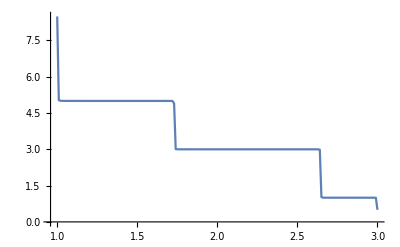

```mathematica
ListPlot[%53,Joined->True]
```